```mathematica
s=DSolve[{ϵ u''[y] + 2 u'[y] + 2 u[y] == 0,u[0]==0,u[1]==1},u[y],y];
```

```mathematica
uex = u[y]/. s[[1]]
```

-(ⅇ^(1/ϵ+(√(1-2 ϵ))/ϵ) (ⅇ^(y (-1/ϵ-(√(1-2 ϵ))/ϵ))-ⅇ^(y (-1/ϵ+(√(1-2 ϵ))/ϵ))))/(-1+ⅇ^((2 √(1-2 ϵ))/ϵ))

```mathematica
pex =Plot[uex/. ϵ -> δ,{y,0,1},PlotStyle-> {Red,Thick},PlotRange -> All];
```

```mathematica
uib = (1-ⅇ^(-y/ϵ));
uoo = ⅇ^(1-y);
uoi = 0.;
```

```mathematica
u1 = ⅇ^(1 - y)- ⅇ^(1-2 y/ϵ);
u2 = ⅇ^(1 - y)- (1+y)ⅇ^(1-2y/ϵ)+ϵ/2((1-y)ⅇ^(1 - y)-ⅇ^(1-2y/ϵ));
```

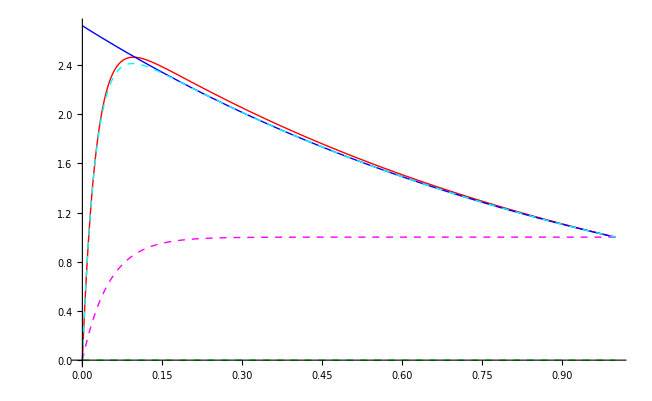

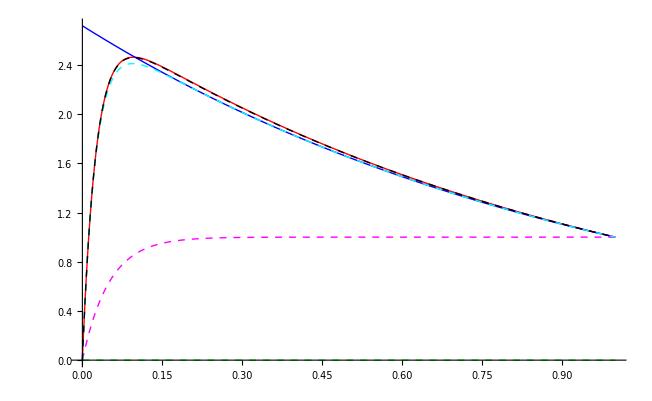

```mathematica
δ= 0.05;
pex =Plot[uex/. ϵ -> δ,{y,0,1},PlotStyle-> {Red,Thick},PlotRange -> All];
poo =Plot[uoo/. ϵ -> δ,{y,0,1},PlotStyle -> {Blue,Thick},PlotRange -> All];
poi =Plot[uoi/. ϵ -> δ,{y,0,1},PlotStyle -> {Green,Dashed,Thick},PlotRange -> All];
pib = Plot[uib/. ϵ -> δ,{y,0,1},PlotStyle -> {Magenta,Dashed,Thick},PlotRange -> All];
po1 = Plot[u1/. ϵ -> δ,{y,0,1},PlotStyle -> {Cyan,Dashed,Thick},PlotRange -> All];
po2 = Plot[u2/. ϵ -> δ,{y,0,1},PlotStyle -> {Black,Dashed,Thick},PlotRange -> All];
Show[pex,poo,poi,pib,po1]
Show[pex,poo,poi,pib,po1,po2,PlotRange -> All]
```

```mathematica
g
```

g

```mathematica
DSolve[{U1''[Y]+2 U1'[Y] == -2 ⅇ (1-ⅇ^(-2 Y)),U1[0]==0},U1[Y],Y]
```

{{U1[Y]→-1/2 ⅇ^(-2 Y) (ⅇ-ⅇ^(1+2 Y)+2 ⅇ Y+2 ⅇ^(1+2 Y) Y+C[1]-ⅇ^(2 Y) C[1])}}

```mathematica
Simplify[%]
```

{{U1[Y]→1/2 ⅇ^(-2 Y) (ⅇ^(1+2 Y) (1-2 Y)-ⅇ (1+2 Y)-C[1]+ⅇ^(2 Y) C[1])}}

```mathematica
DSolve[{V1'[y]+V1[y] == -1/2 ⅇ^(1- y),V1[1]==0},V1[y],y]
```

{{V1[y]→-1/2 ⅇ^(1-y) (-1+y)}}

```mathematica
Simplify[uex]
```

(ⅇ^(-((-1+y) (1+√(1-2 ϵ)))/ϵ) (-1+ⅇ^((2 y √(1-2 ϵ))/ϵ)))/(-1+ⅇ^((2 √(1-2 ϵ))/ϵ))